## Viral Evolution

### What is the nature of the space of all possible viruses

```mathematica
Module[{gk2r2,embedding},
gk2r2=WeaklyConnectedGraphComponents[
Import[CloudObject[["https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c"](https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c)]],
AspectRatio->2/3][[1]];
SeedRandom[12345];
embedding=Map[#+RandomReal[20,2]&,
GraphEmbedding[gk2r2]];
Graph[gk2r2,EdgeStyle->Directive[Hue[0.6,0.4,0.5,.6],Opacity[.15]],
VertexStyle->GrayLevel[.3],VertexCoordinates->embedding]
]
```

```mathematica
gk2r2=WeaklyConnectedGraphComponents[
Import[CloudObject[["https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c"](https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c)]],
AspectRatio->2/3][[1]];
```

```mathematica
gk2r2
```

-Graphics-

```mathematica
{VertexConnectivity[gk2r2], EdgeConnectivity[gk2r2], GraphDensity[gk2r2], GraphLinkEfficiency[gk2r2], GraphReciprocity[gk2r2]}
```

{0,0,277/414348,-∞,0}

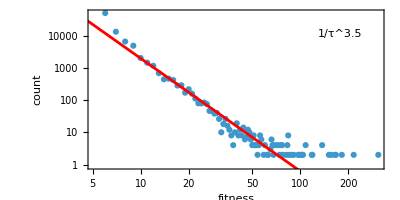

```mathematica
Module[{data=List@@@Normal[KeySort[Counts[Values[Uncompress@]+1]]],fit,b=-3.5},fit=FindFit[Take[data,{10,50}],a τ^b,{a},τ];Show[ListLogLogPlot[data,Frame->True,FrameLabel->{"fitness", "count"},AspectRatio->1/2,Epilog->{Inset[Text[NumberForm[τ^b,3]],Scaled[{.85,.85}]],
Inset[Graphics[{Red,Thick,Line[{{0,0},{.1,0}}]}],Scaled[{.75,.85}]]
}],LogLogPlot[Evaluate[a τ^b /.fit],{τ,1,Max[First/@data]},PlotStyle->Red]]]
```

### Relevant papers

https://nextstrain.org/sars-cov-2/forecasts

https://bedford.io/pdfs/papers/kistler-atlas-viral-evolution.pdf

https://nextstrain.org/ncov/gisaid/global/6m

### Gene Transfer

```mathematica
SeedRandom[666680 + 11];
hevo = NestList[
Function[evosteps, 
If[!AllSameBy[evosteps,  #fitness&],
Table[First[MaximalBy[evosteps, #fitness&]], Length[evosteps]],
newevosteps = 
With[{nr = {{"[◼]", "RandomRuleMutation"}}[#rule]},
<|"rule"->nr, "fitness"->{{"[◼]", "TestLifetime"}}[nr]|>]&/@ evosteps;
MapThread[If[#2["fitness"] == -Infinity, #1, If[0 <= #2["fitness"] - #fitness<= 1, #2, #]]&, {evosteps, newevosteps}]
]], Table[<|"rule"-> {109636419052937157723438118980837975564,4,1}, "fitness"-> {{"[◼]", "TestLifetime"}}[{109636419052937157723438118980837975564,4,1}]|>, 2], 2000];
```

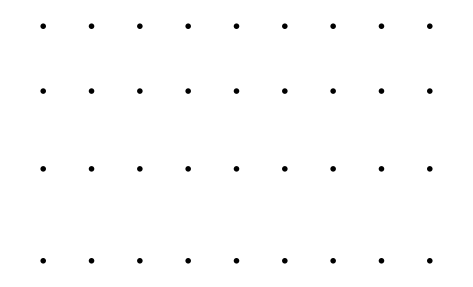

```mathematica
GraphicsGrid[
Partition[
MapIndexed[
GraphicsRow[
Function[{evosteps, index},
With[{largest = If[Length[#] == 1, First[#], -1]&[MaximalBy[evosteps,#fitness&]]},
Rasterize[ArrayPlot[
CellularAutomaton[#rule, {{1}, 0}, 
{Which[
index <= 9, 15,
9<index<= 18, 20,
18<index<= 27, 24,
True, 30
], {-3, 3}}], 
ImageSize->{20,Automatic},Mesh->False,FrameStyle->Directive[Thickness[.1],Mesh->False, If[# === largest, RGBColor[0,0.74,0], GrayLevel[.4]]],
ColorRules->{0->GrayLevel[0.15],1->Hue[0.06, 1, 1],2->Hue[0.14, 0.81, 0.99],3->Hue[0.73, 1, 1]}, Background->GrayLevel[.14]]]&/@ evosteps]][First[#1], #2[[1]]], Spacings->.5]&, GatherBy[Take[hevo, 1000], #[[All, "fitness"]]&]], 9], Spacings->{8, Automatic}]
```

```mathematica
SeedRandom[666680 + 1];
evo = NestList[
Function[evosteps, 
newevosteps = 
With[{nr = {{"[◼]", "RandomRuleMutation"}}[#rule]},
<|"rule"->nr, "fitness"->{{"[◼]", "TestLifetime"}}[nr]|>]&/@ evosteps;
MapThread[If[#2["fitness"] == -Infinity, #1, If[0 <= #2["fitness"] - #fitness<= 1, #2, #]]&, {evosteps, newevosteps}]
], Table[<|"rule"-> {109636419052937157723438118980837975564,4,1}, "fitness"-> {{"[◼]", "TestLifetime"}}[{109636419052937157723438118980837975564,4,1}]|>, 2], 2000];
```

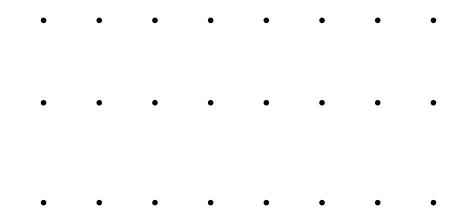

```mathematica
GraphicsGrid[
Partition[
MapIndexed[
GraphicsRow[
Function[{evosteps, index},
With[{largest = If[Length[#] == 1, First[#], -1]&[MaximalBy[evosteps,#fitness&]]},
ArrayPlot[
CellularAutomaton[#rule, {{1}, 0}, 
{Which[
index <= 8, 15,
8<index<= 16, 20,
16<index<= 24, 24,
True, 30
], {-3, 3}}], 
ImageSize->{20,Automatic},Mesh->False, ColorRules->{0->GrayLevel[0.15],1->Hue[0.06, 1, 1],2->Hue[0.14, 0.81, 0.99],3->Hue[0.73, 1, 1]}]&/@ evosteps]][First[#1], #2[[1]]], Spacings->.5]&, GatherBy[Take[evo, 1000], #[[All, "fitness"]]&]], 8], Spacings->{8, Automatic}]
```

```mathematica
SeedRandom[666680 + 11];
hevo = NestList[
Function[evosteps, 
If[!AllSameBy[evosteps,  #fitness&],
Table[First[MaximalBy[evosteps, #fitness&]], Length[evosteps]],
newevosteps = 
With[{nr = {{"[◼]", "RandomRuleMutation"}}[#rule]},
<|"rule"->nr, "fitness"->{{"[◼]", "TestLifetime"}}[nr]|>]&/@ evosteps;
MapThread[If[#2["fitness"] == -Infinity, #1, If[0 <= #2["fitness"] - #fitness<= 1, #2, #]]&, {evosteps, newevosteps}]
]], Table[<|"rule"-> {109636419052937157723438118980837975564,4,1}, "fitness"-> {{"[◼]", "TestLifetime"}}[{109636419052937157723438118980837975564,4,1}]|>, 2], 2000];
```

```mathematica
drf1 = DimensionReduction[IntegerDigits[#rule[[1]],4,64]&/@Catenate[GatherBy[hevo, #[[All, "fitness"]]&][[All, 1]]],Method->"TSNE"];
drs3 = drf1[IntegerDigits[#rule[[1]],4,64]]&/@ GatherBy[hevo, #[[All, "fitness"]]&][[All, 1, 1]];
drs4 = drf1[IntegerDigits[#rule[[1]],4,64]]&/@ GatherBy[hevo, #[[All, "fitness"]]&][[All, 1, 2]];
```

```mathematica
co3 = MapThread[Callout[#1, Pane[ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#2["rule"], {{1}, 0},{{"[◼]", "TestLifetime"}}[ #2["rule"]] + 1],ColorRules->{0->GrayLevel[0.15],1->Hue[0.06, 1, 1],2->Hue[0.14, 0.81, 0.99],3->Hue[0.73, 1, 1]} , 
ImageSize->{Automatic, 8Sqrt[1+{{"[◼]", "TestLifetime"}}[#2["rule"]]]}]], Background->None]&, {drs3, GatherBy[hevo, #[[All, "fitness"]]&][[All, 1, 1]]}];
```

```mathematica
co4 = MapThread[Callout[#1, Pane[ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#2["rule"], {{1}, 0},{{"[◼]", "TestLifetime"}}[ #2["rule"]] + 1],ColorRules->{0->GrayLevel[0.15],1->Hue[0.06, 1, 1],2->Hue[0.14, 0.81, 0.99],3->Hue[0.73, 1, 1]} , 
ImageSize->{Automatic, 10Sqrt[1+{{"[◼]", "TestLifetime"}}[#2["rule"]]]}]], Background->None]&, {drs4, GatherBy[hevo, #[[All, "fitness"]]&][[All, 1, 2]]}];
```

```mathematica
ListLinePlot[{co3, co4}, Frame->True,Axes->False, PlotHighlighting->None, PlotStyle->{ RGBColor[0.8300000000000001, 0.31, 0.],RGBColor[0.52, 0.65, 0.]}, Mesh->All, FrameTicks->False]
```

-Graphics-

```mathematica
drf1 = DimensionReduction[IntegerDigits[#rule[[1]],4,64]&/@Catenate[GatherBy[evo, #[[All, "fitness"]]&][[All, 1]]],Method->"TSNE"];
drs1 = drf1[IntegerDigits[#rule[[1]],4,64]]&/@ GatherBy[evo, #[[All, "fitness"]]&][[All, 1, 1]];
drs2 = drf1[IntegerDigits[#rule[[1]],4,64]]&/@ GatherBy[evo, #[[All, "fitness"]]&][[All, 1, 2]];
```

```mathematica
co1 = MapThread[Callout[#1, Pane[ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#2["rule"], {{1}, 0},{{"[◼]", "TestLifetime"}}[ #2["rule"]] + 1],ColorRules->{0->GrayLevel[0.15],1->Hue[0.06, 1, 1],2->Hue[0.14, 0.81, 0.99],3->Hue[0.73, 1, 1]} , 
ImageSize->{Automatic, 10Sqrt[1+{{"[◼]", "TestLifetime"}}[#2["rule"]]]}]], Background->None]&, {drs1, GatherBy[evo, #[[All, "fitness"]]&][[All, 1, 1]]}];
```

```mathematica
co2 = MapThread[Callout[#1, Pane[ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#2["rule"], {{1}, 0},{{"[◼]", "TestLifetime"}}[ #2["rule"]] + 1],ColorRules->{0->GrayLevel[0.15],1->Hue[0.06, 1, 1],2->Hue[0.14, 0.81, 0.99],3->Hue[0.73, 1, 1]} , 
ImageSize->{Automatic, 10Sqrt[1+{{"[◼]", "TestLifetime"}}[#2["rule"]]]}]], Background->None]&, {drs2, GatherBy[evo, #[[All, "fitness"]]&][[All, 1, 2]]}];
```

```mathematica
ListLinePlot[{co1, co2}, Axes->False, PlotHighlighting->None, Mesh->All, Frame->True, FrameTicks->False]
```

-Graphics-

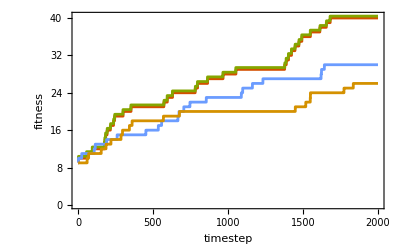

```mathematica
ListStepPlot[{hevo[[All, 1, "fitness"]],hevo[[All, 2, "fitness"]]+.4, evo[[All, 1, "fitness"]], 
evo[[All, 2, "fitness"]]}, PlotStyle->{ RGBColor[0.8300000000000001, 0.31, 0.],RGBColor[0.52, 0.65, 0.], RGBColor[0.42, 0.61, 1.], RGBColor[0.8300000000000001, 0.5700000000000001, 0.]}, Frame->{True, True, False, False},FrameLabel->{"timestep", "fitness"}, PlotLegends->SwatchLegend[{White, White}, {"hierarchical", "regular"},LegendMarkers->{Image[Graphics[{RGBColor[0.52, 0.65, 0.] ,  Rectangle[{0, 1/2}, {1, 1}],RGBColor[0.8300000000000001, 0.31, 0.]  , Rectangle[{0, 0}, {1, 1/2}]}]], Image[Graphics[{ RGBColor[0, 0.41000000000000003, 1.],  Rectangle[{0, 1/2}, {1, 1}],  RGBColor[0.92, 0.59, 0], Rectangle[{0, 0}, {1, 1/2}]}]]}, LegendMarkerSize->15] ]
```

### Recombination of initial condition

```mathematica
RandomChoice[Delete[Range[0, k - 1], #+1]]&
```

```mathematica
shuffleevo = NestList[
Function[{init, fitness}, 
newinit = MapAt[RandomChoice[Delete[Range[0, k - 1], #+1]]&, init, RandomInteger[{1, Length@init}]];
inits = Join@@@Permutations[Partition[newinit, UpTo[5]]];
newfitness = Min[TestCALifeTime[CellularAutomaton[ru, {#, 0}, {115, All}]]&/@ inits];
If[newfitness>= fitness, {newinit, newfitness}, {init, fitness}]]@@#&,
{CenterArray[{1},20], 1}, 1000];
```

```mathematica
(*Join@@@*)Permutations[Partition[newinit, UpTo[5]]]
```

{{{1,0,0,0,1},{0,0,0,0,0}},{{0,0,0,0,0},{1,0,0,0,1}}}

```mathematica
CellularAutomaton[30, {{}}]
```

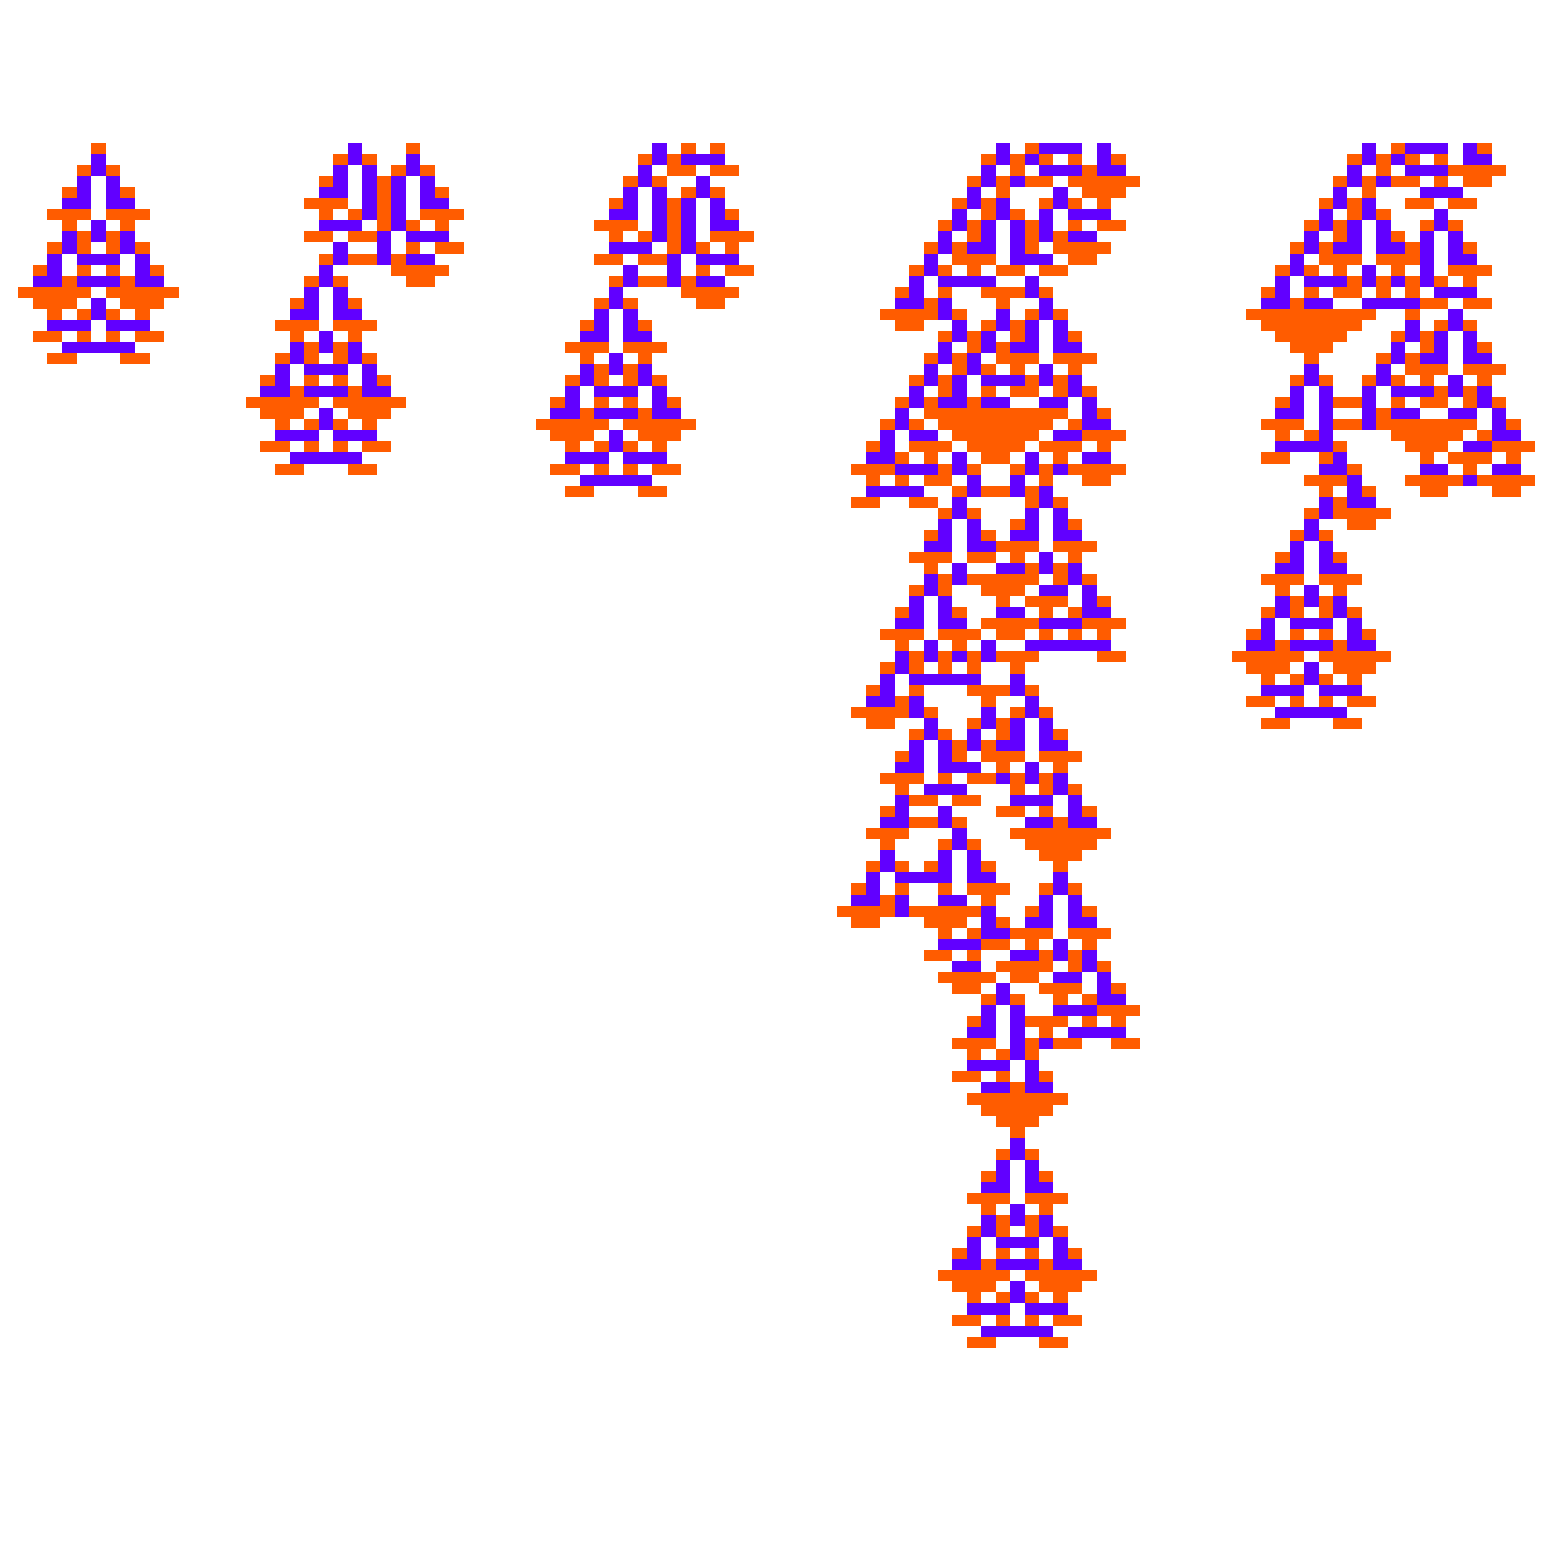

```mathematica
GraphicsRow[ArrayPlot[CellularAutomaton[ru,{#[[1, 1]], 0},{115, Automatic}]]&/@ GatherBy[shuffleevo, Last]]
```

```mathematica
Partition[#[[1, 1]], UpTo[5]]&/@ GatherBy[shuffleevo, Last]
```

{{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,1,0,1},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,1,2,0},{0,0,1,0,1},{0,0,0,0,0},{0,0,0,0,0}},{{0,2,1,2,0},{0,0,1,0,1},{0,0,0,0,0},{0,0,0,0,0}},{{0,2,1,2,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

```mathematica
Length/@(Permutations[Partition[#[[1, 1]], UpTo[5]]]&/@GatherBy[shuffleevo, Last])
```

{4,4,12,12,4}

```mathematica
Length/@(Join@@@Permutations[Partition[#[[1, 1]], UpTo[5]]]&/@GatherBy[shuffleevo, Last])
```

{4,4,12,12,4}

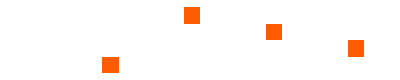
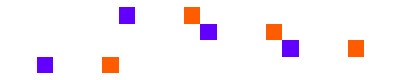
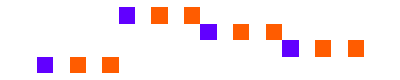
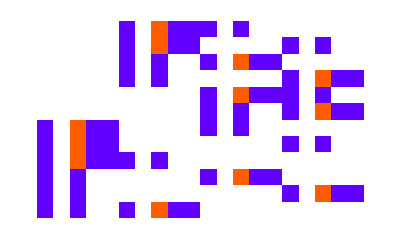
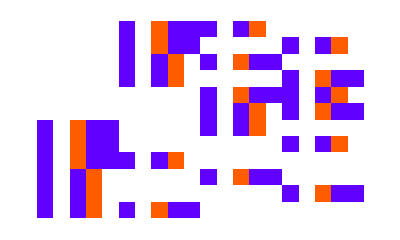

```mathematica
Map[ArrayPlot, Join@@@Permutations[Partition[#[[1, 1]], UpTo[5]]]&/@GatherBy[shuffleevo, Last]]
```

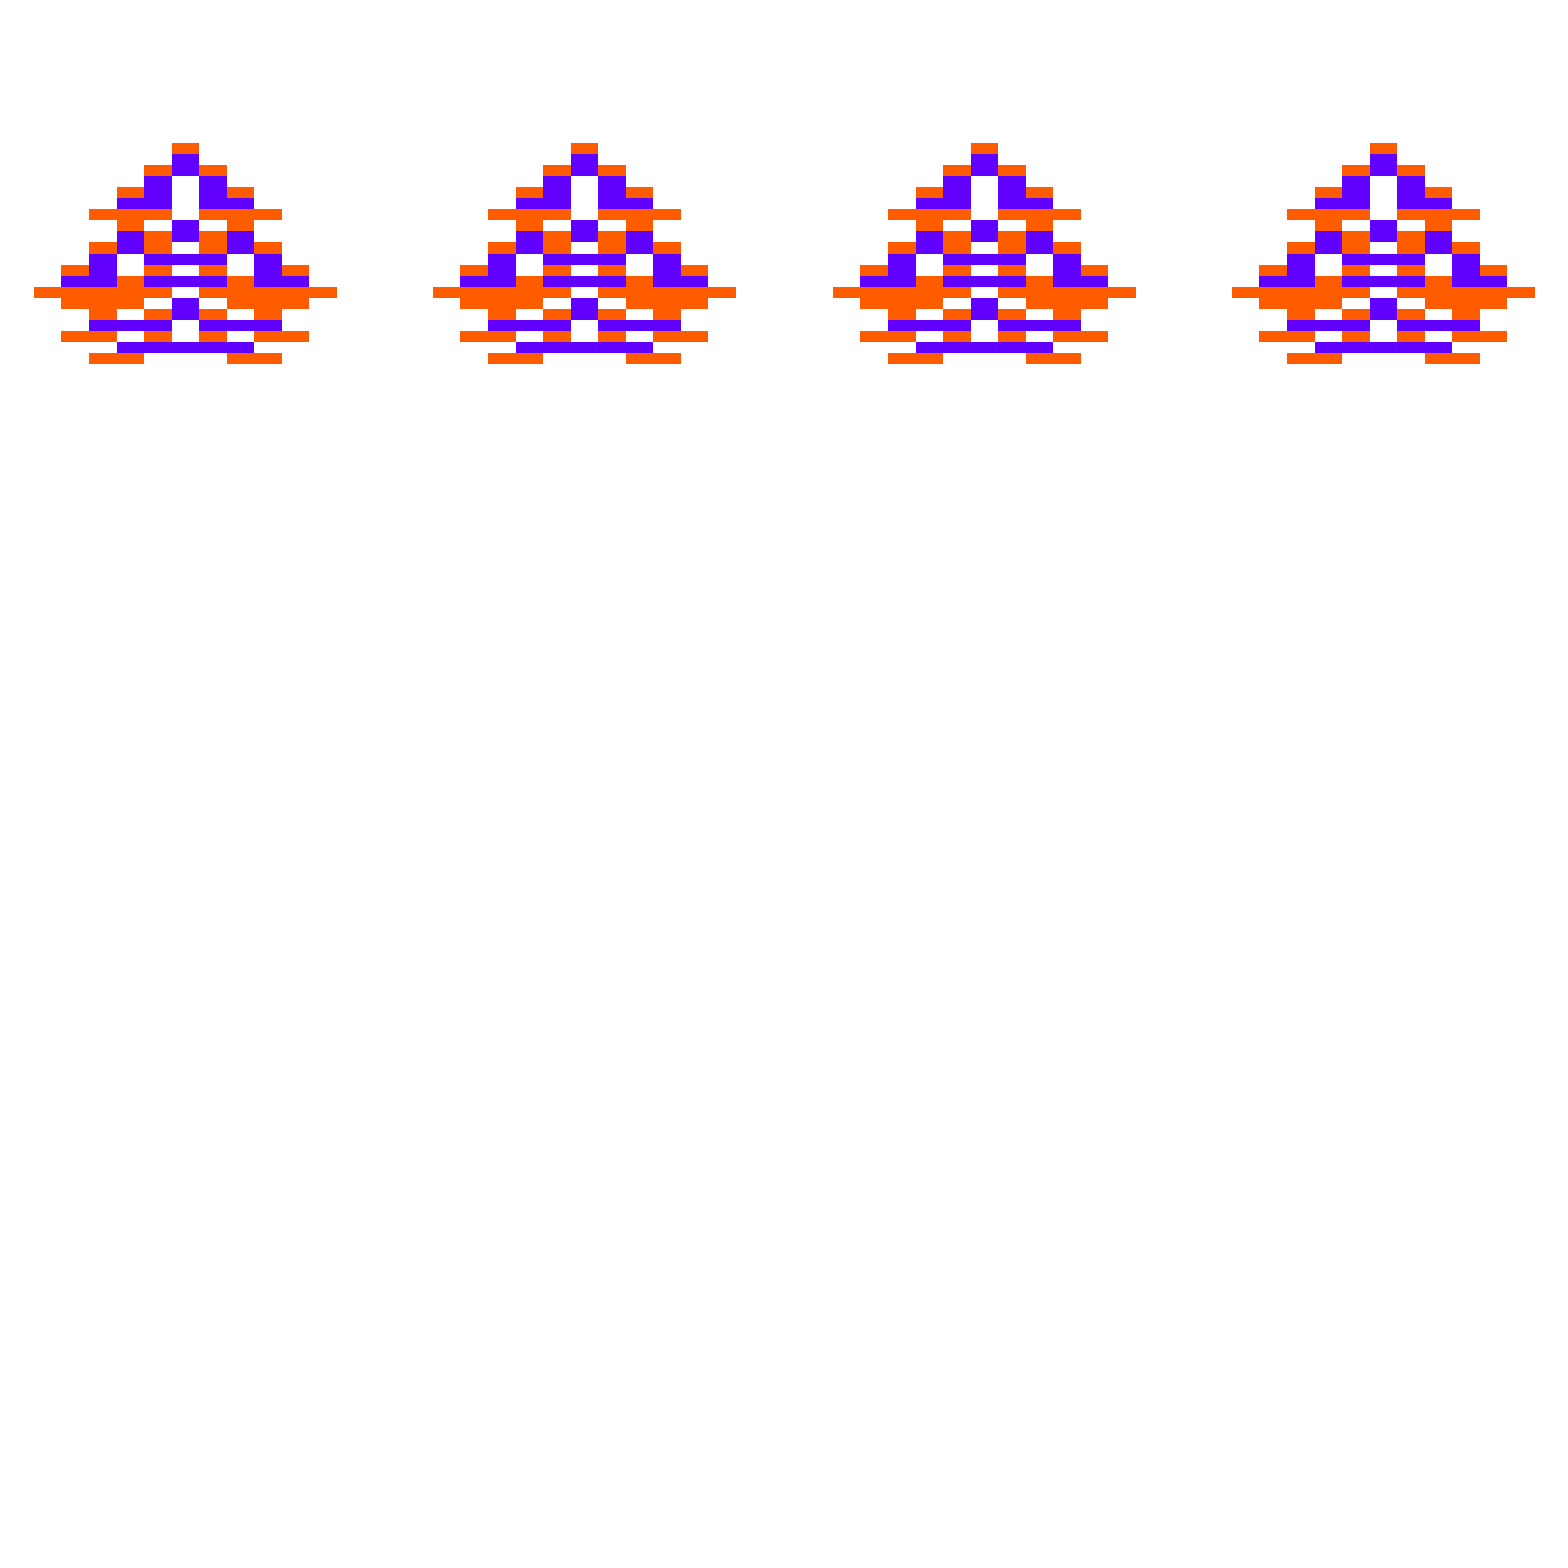
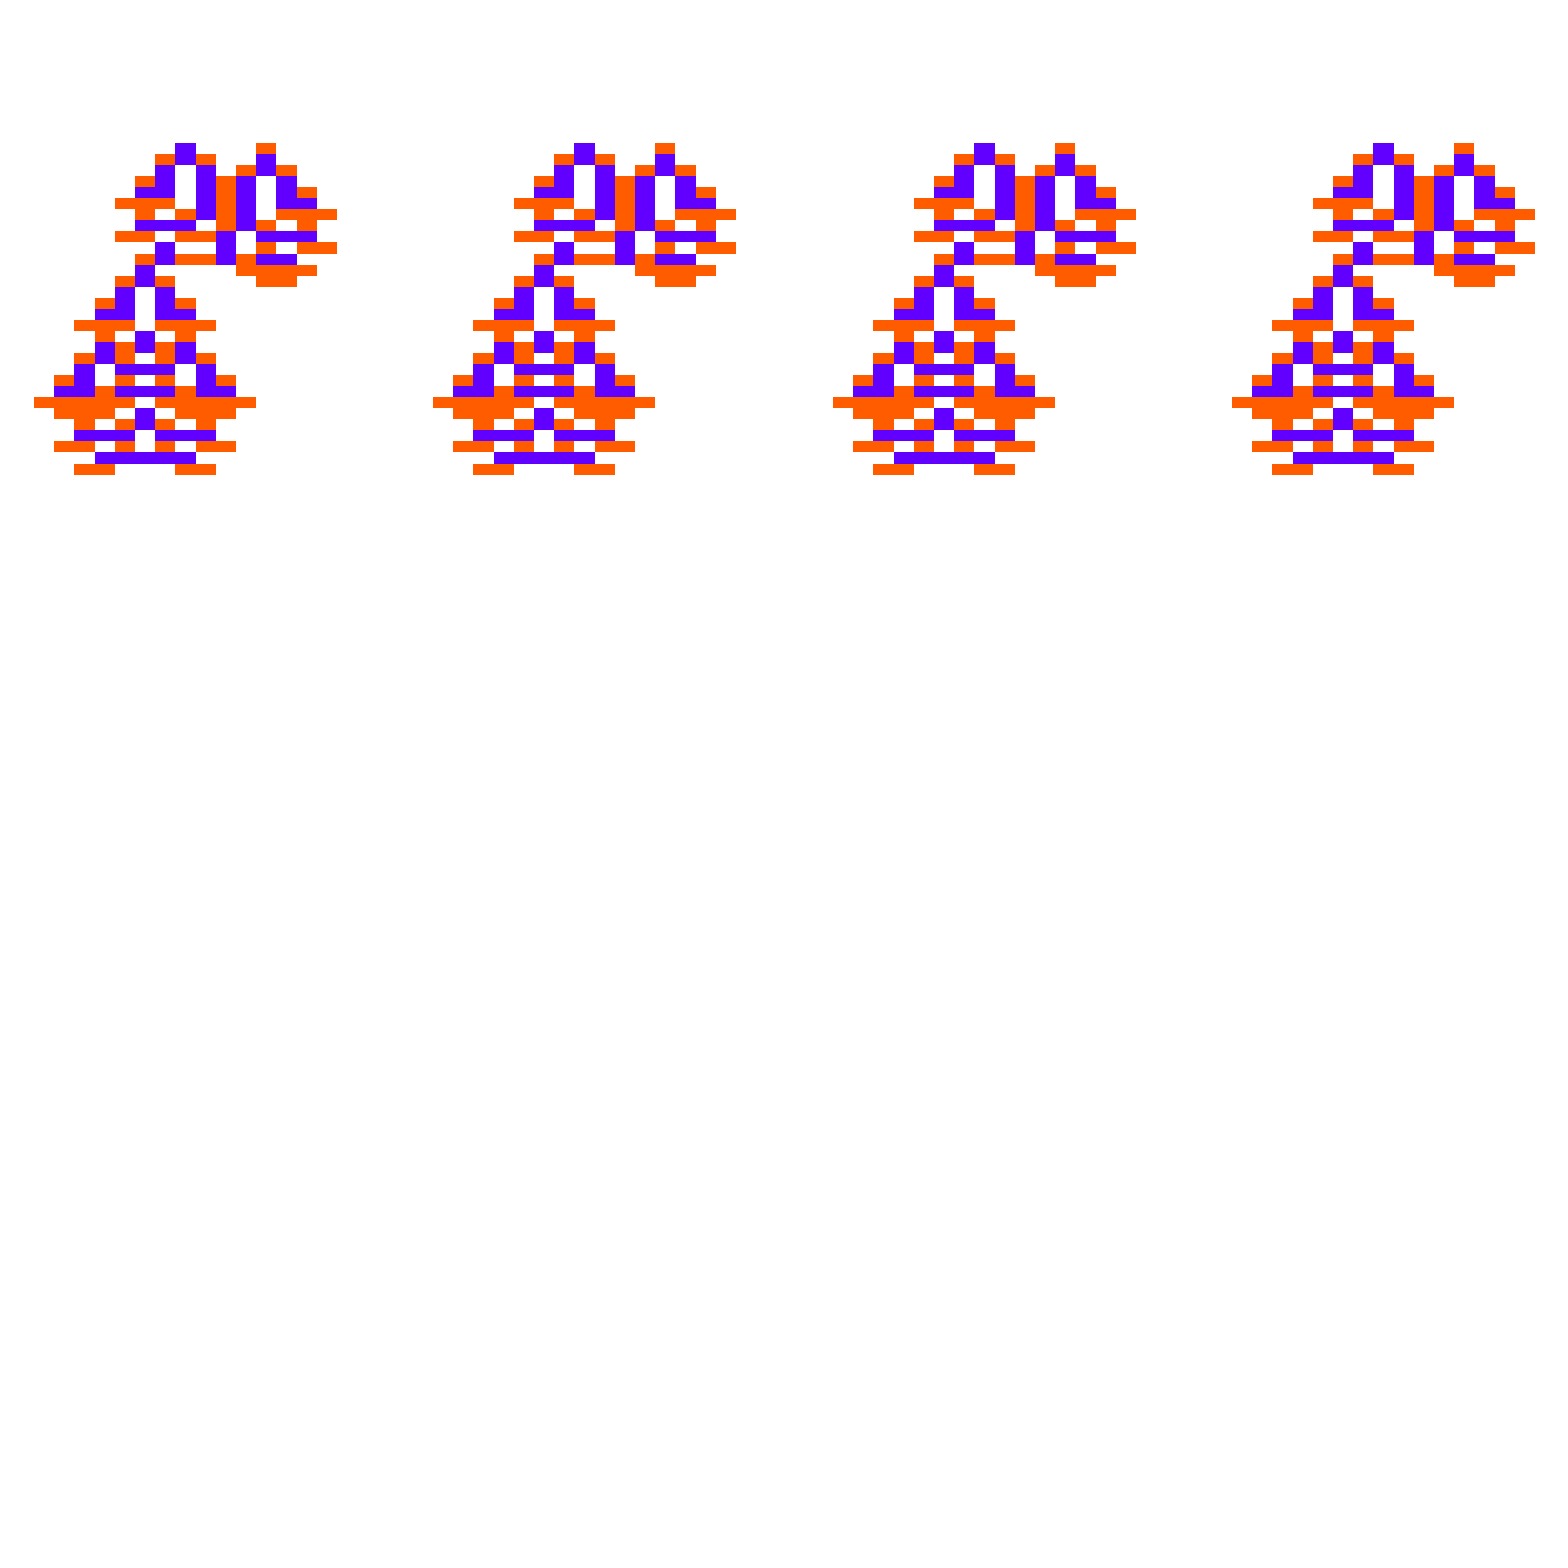
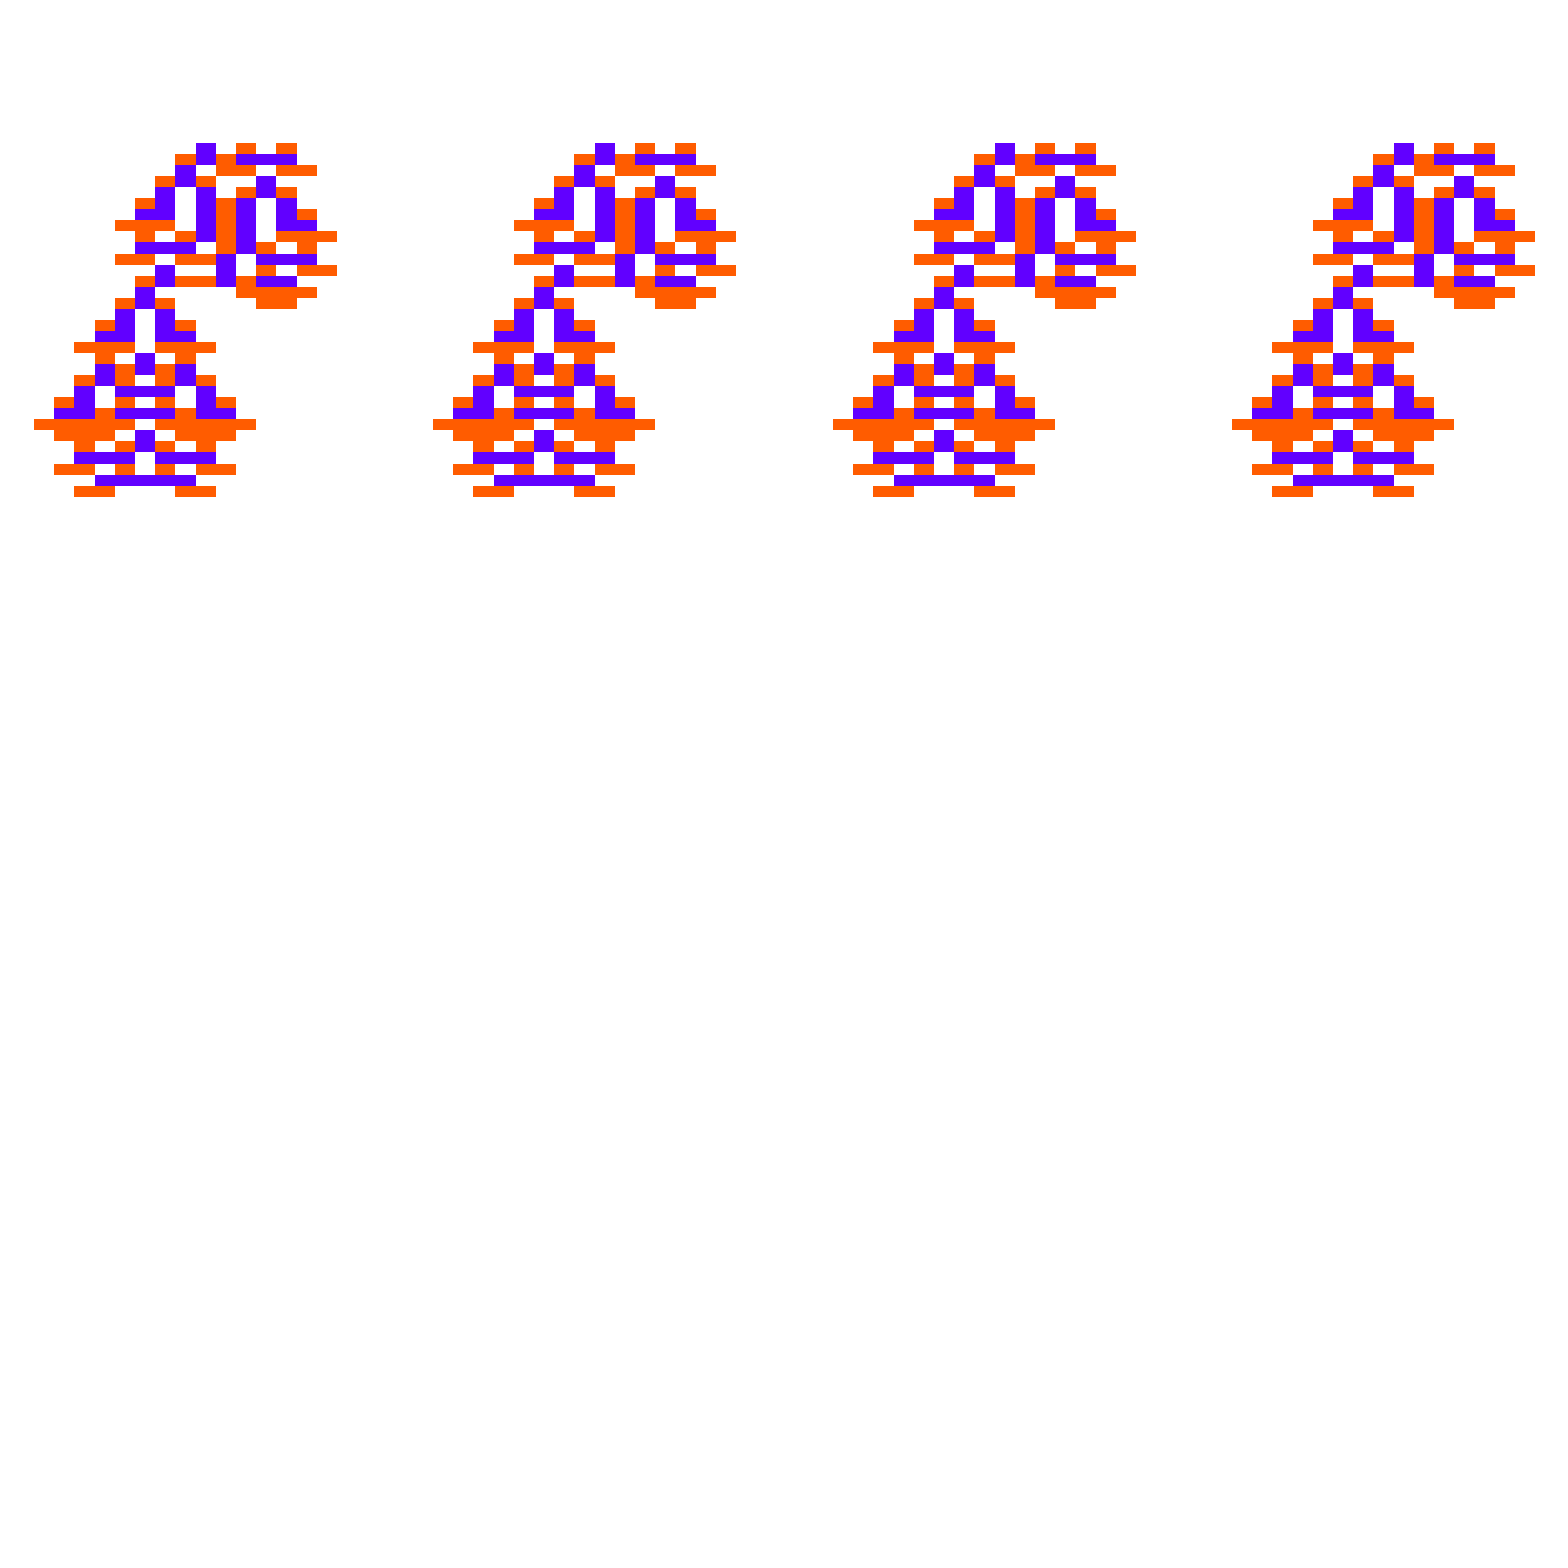
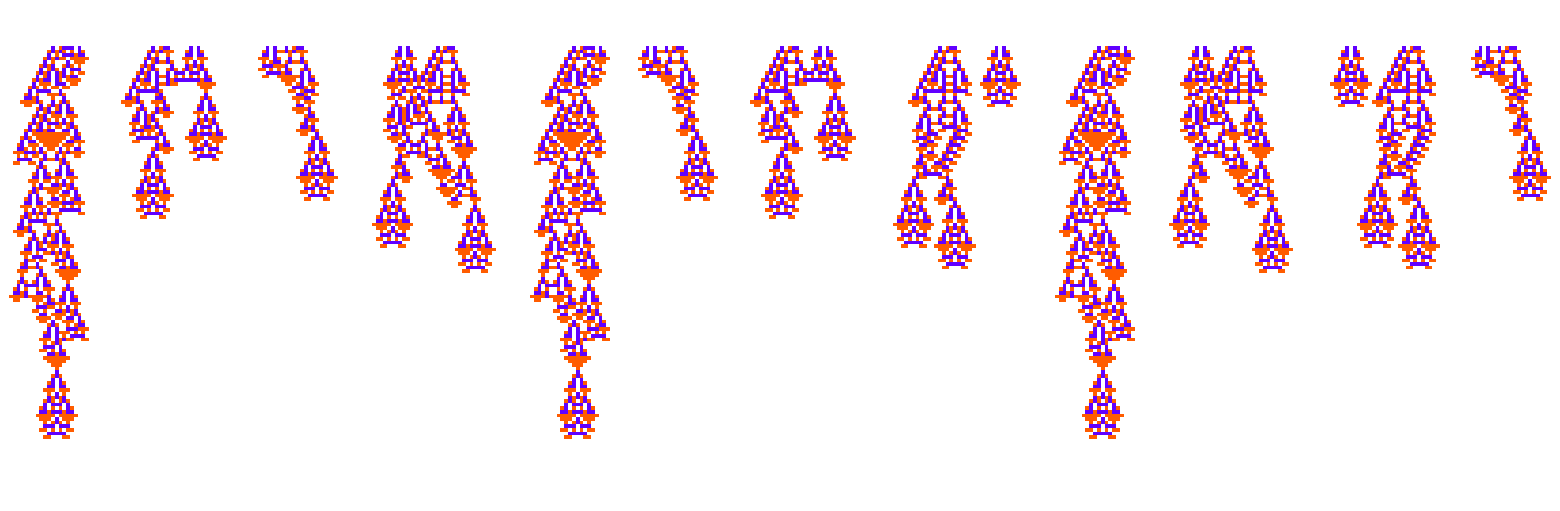
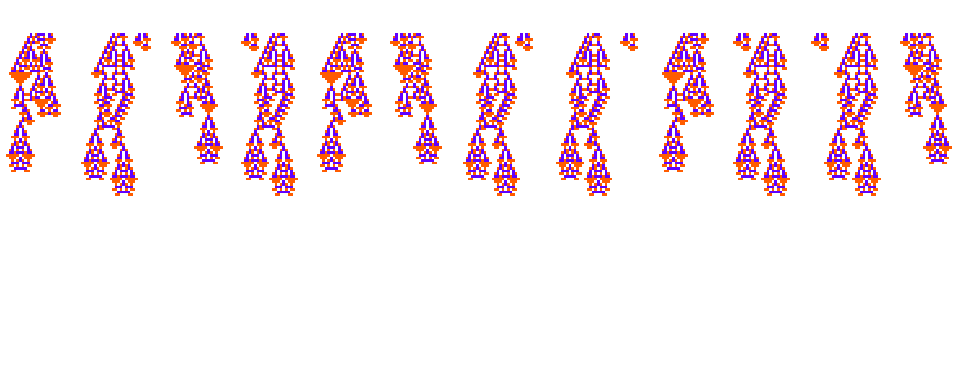

```mathematica
GraphicsRow[ArrayPlot[CellularAutomaton[ru,{#,0},{115, Automatic}]]&/@Join@@@Permutations[Partition[#[[1, 1]], UpTo[5]]]]&/@ GatherBy[shuffleevo, Last]
```